```mathematica
ClearAll["Global`*"]
```

```mathematica
c={0.5,0.5};
r=0.2;
d=0;
L=1.2553455316455193;
```

```mathematica
norm[θ_]:=θ-2π Floor[θ/(2π)]
```

```mathematica
ys[x_]:=c+r{Cos[2π x/L],Sin[2π x /L]}
U[x_]:={d Cos[2π 3 x/L] Cos[2π x/L],d Cos[2π 3x /L]Sin[2π x /L]}
X[x_]:=ys[x]+U[x]
ψ[x_]:=-ArcTan[X'[x][[1]],X'[x][[2]]]
ψ0[x_]:=-2 π x/L
dψ[x_]:=norm[ψ[x]-ψ0[x]]
ν[x_]:=Norm[X'[x]]
l[x_]:=NIntegrate[Sqrt[g[y]],{y,0,x}]

e[x_]:=X'[x]
g[x_]:=e[x].e[x]
gc[x_]:=1/g[x]
n[x_]:={-e[x][[2]],e[x][[1]]}/Sqrt[g[x]]
b[x_]:=n[x].e'[x]
H[x_]:=1/2 gc[x]b[x]
```

```mathematica
(*check X*)
```

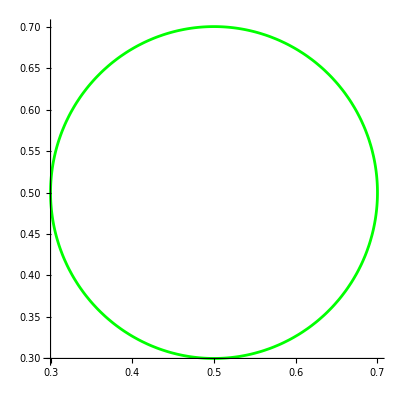

```mathematica
plotexX =ParametricPlot[X[x],{x,0,L},PlotStyle->Green]
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/snapshots/csv/U_n_12_200.csv"][[2;;]];
t=Table[{t[[i,3]],t[[i,2]]},{i,2,Length[t]}]
tsm=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/snapshots/csv/U_n_12_sm_200.csv"][[2;;]];
tsm=Table[{tsm[[i,3]],tsm[[i,2]]},{i,2,Length[tsm]}]
```

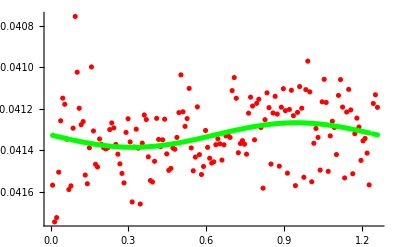

```mathematica
Show[ListPlot[t,PlotStyle->Red],ListPlot[tsm,PlotStyle->Green]]
```

Show::gcomb: Could not combine the graphics objects in Show[plotexX,].

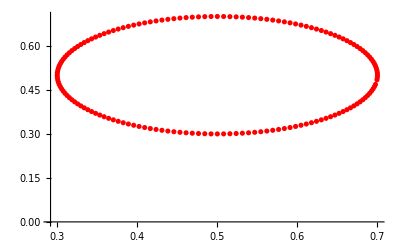
Show[plotexX,-Graphics-]

```mathematica
Show[plotexX,plotnumX]
```

```mathematica
(*check nu*)
```

```mathematica
plotexν=ParametricPlot[{l[x],Norm[e[x]]},{x,0,L},PlotStyle->Green]
```

-Graphics-

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/snapshots/csv/nu_n_12_20.csv"][[2;;]];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

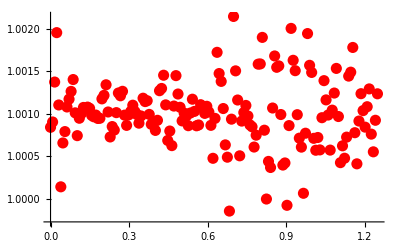

```mathematica
plotnumν=ListPlot[t,PlotStyle->{Red,PointSize->0.02}]
```

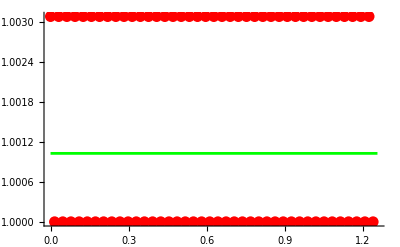

```mathematica
Show[plotnumν,plotexν,PlotRange->Full]
```

```mathematica
(*check psi*)
```

```mathematica
plotexψ=ParametricPlot[{l[x],norm[-ArcTan[e[x][[1]],e[x][[2]]]-ψ0[x]]},{x,0,L},PlotStyle->Green]
```

-Graphics-

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/snapshots/csv/dpsi_n_12_10.csv"][[2;;]];
t=Table[{t[[i,2]],norm[t[[i,1]]]},{i,2,Length[t]}]
```

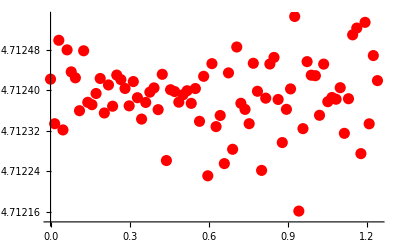

```mathematica
plotnumψ=ListPlot[t,PlotStyle->{Red,PointSize->0.02},Plot]
```

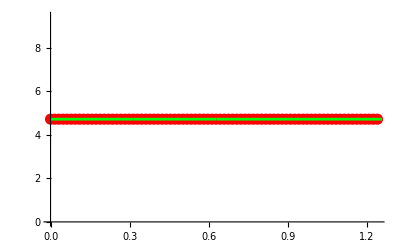

```mathematica
Show[plotnumψ,plotexψ]
```

```mathematica
(*check mu*)
```

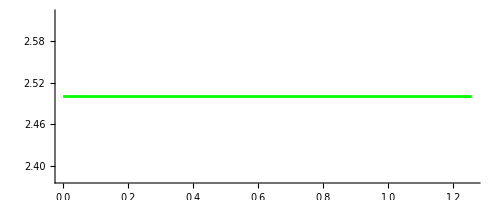

```mathematica
plotexμ=ParametricPlot[{l[x],H[x]},{x,0,L},PlotStyle->Green]
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/snapshots/csv/mu_n_12_130.csv"][[2;;]];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

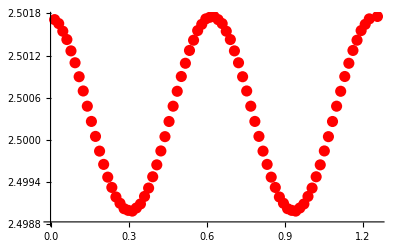

```mathematica
plotnumμ=ListPlot[t,PlotStyle->{Red,PointSize->0.02}]
```

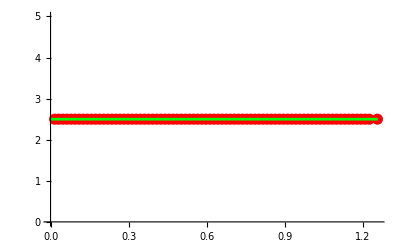

```mathematica
Show[plotnumμ,plotexμ]
```